```mathematica
d[k_]:=Flatten@ToExpression@StringSplit[Import["./BENCHMARK"][[k]],","]
```

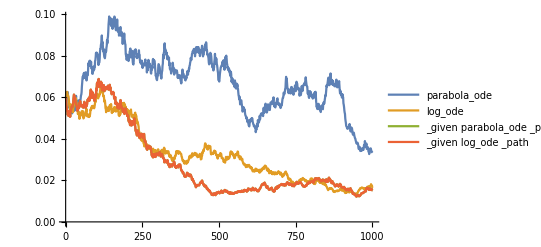

```mathematica
ListLinePlot[Table[d[2*k+1],{k,1,4}],PlotLegends->Table[d[2*k][[1]],{k,1,4}],PlotRange->Full]
```